```mathematica
Gam[x_,y_]:=-Series[1-I-I*Cos[x]-I*Cos[y]+I*(1/4)Cos[2y],{x,0,6},{y,0,8}]
```

```mathematica
Gam[x,y]//ExpandAll
```

(-(1-(11 ⅈ)/4)-(ⅈ y^4)/8+(ⅈ y^6)/48-(ⅈ y^8)/640+O[y]^9)-(ⅈ x^2)/2+(ⅈ x^4)/24-(ⅈ x^6)/720+O[x]^7

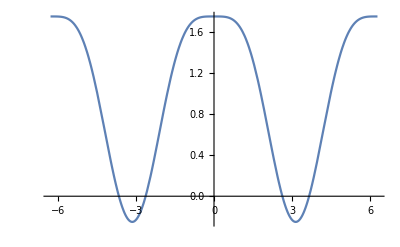

```mathematica
Plot[1+Cos[y]-(1/4)Cos[2y],{y,-2Pi,2Pi}]
```

```mathematica
Plot3D[Abs[1-I-I*Cos[x]-I*Cos[y]+I*(1/4)Cos[2y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
RulePhi={Cos[x]->(1/2)(E^(I*x)+E^(-I*x)),
Cos[2x]->(1/2)(E^(2I*x)+E^(-2I*x)),
Cos[y]->(1/2)(E^(I*y)+E^(-I*y)),
Cos[2y]->(1/2)(E^(2I*y)+E^(-2I*y))};
```

```mathematica
FindMaximum[Abs[1-I-I*Cos[x]-I*Cos[y]+I*(1/4)Cos[2y]],{{x,0.0001},{y,0.0001}}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.92617,{x→9.73176×10^-9,y→0.000100032}}

```mathematica
PhiHat[x_,y_]:=(1-I-I*Cos[x]-I*Cos[y]+I*(1/4)Cos[2y])
```

```mathematica
PhiHat[0,0]
```

1-(11 ⅈ)/4

```mathematica
PhiHat[0,0]
```

1

```mathematica
PhiHat[x,y]/.RulePhi//ExpandAll
```

(60/137+(28 ⅈ)/137)+(22/137-(8 ⅈ)/137) ⅇ^(-ⅈ x)+(22/137-(8 ⅈ)/137) ⅇ^(ⅈ x)+(22/137-(8 ⅈ)/137) ⅇ^(-ⅈ y)+(22/137-(8 ⅈ)/137) ⅇ^(ⅈ y)-(11/274-(2 ⅈ)/137) ⅇ^(-2 ⅈ y)-(11/274-(2 ⅈ)/137) ⅇ^(2 ⅈ y)

```mathematica
PhiHat[0,0]
```

1

```mathematica
PhiHat[x,y]
```

(16/137+(44 ⅈ)/137) ((1-ⅈ)-ⅈ Cos[x]-ⅈ Cos[y]+1/4 ⅈ Cos[2 y])

```mathematica
Series[Log[PhiHat[x,y]/PhiHat[0,0]],{x,0,6},{y,0,8}]
```

(-(11/274-(2 ⅈ)/137) y^4+(11/1644-ⅈ/411) y^6-(3607/3003040-(577 ⅈ)/750760) y^8+O[y]^9)+(-(22/137-(8 ⅈ)/137)-(105/18769-(88 ⅈ)/18769) y^4+(35/37538-(44 ⅈ)/56307) y^6-(9301/41141648-(8447 ⅈ)/25713530) y^8+O[y]^9) x^2+((247/112614+(254 ⅈ)/56307)-(1629/10285412-(5314 ⅈ)/7714059) y^4+(543/20570824-(2657 ⅈ)/23142177) y^6-(993719/338184346560-(2739629 ⅈ)/42273043320) y^8+O[y]^9) x^4+((271201/462843540+(4489 ⅈ)/115710885)+(433729/8454608664+(680519 ⅈ)/15852391245) y^4-(433729/50727651984+(680519 ⅈ)/95114347470) y^6+(1576546403/277987532872320+(1061121563 ⅈ)/173742208045200) y^8+O[y]^9) x^6+O[x]^7